# Series

| Seriespaclet:ref/Series[f,{x,x_0,n}]
generates a power series expansion for f about the point x=x_0 to order (x-x_0)^n. 
 | Seriespaclet:ref/Series[f,{x,x_0,n_x},{y,y_0,n_y},…]
successively finds series expansions with respect to x, then y, etc.

Details and Options

Seriespaclet:ref/Series can construct standard Taylor series, as well as certain expansions involving negative powers, fractional powers, and logarithms.

Seriespaclet:ref/Series detects certain essential singularities. Onpaclet:ref/On[Series::esss] makes Seriespaclet:ref/Series generate a message in this case.

Seriespaclet:ref/Series can expand about the point x=∞.

Seriespaclet:ref/Series[f,{x,0,n}] constructs Taylor series for any function f according to the formula f(0)+f'(0)x+f''(0)x^2/2+…f^(n)(0)x^n/n!.

Seriespaclet:ref/Series effectively evaluates partial derivatives using Dpaclet:ref/D. It assumes that different variables are independent.

The result of Seriespaclet:ref/Series is usually a SeriesDatapaclet:ref/SeriesData object, which you can manipulate with other functions.

Normalpaclet:ref/Normal[series] truncates a power series and converts it to a normal expression.

SeriesCoefficientpaclet:ref/SeriesCoefficient[series,n] finds the coefficient of the n^th-order term.

## Examples (45)

### Basic Examples (3)

Power series for the exponential function around x=0:

```mathematica
Series[Exp[x],{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

Convert to a normal expression:

```mathematica
Normal[%]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800

Power series of an arbitrary function around x=a:

```mathematica
Series[f[x],{x,a,3}]
```

f[a]+f'[a] (x-a)+1/2 f''[a] (x-a)^2+1/6 f^(3)[a] (x-a)^3+O[x-a]^4

```mathematica
Series[Cos[x]/x,{x,0,10}]
```

1/x-x/2+x^3/24-x^5/720+x^7/40320-x^9/3628800+O[x]^11

In any operation on series, only appropriate terms are kept:

```mathematica
1/(1+%)+%^2
```

1/x^2-1+x-(2 x^2)/3+(3 x^3)/2-(92 x^4)/45+(65 x^5)/24-(1154 x^6)/315+(3571 x^7)/720-(95132 x^8)/14175+(366113 x^9)/40320+O[x]^10

### Scope (10)

#### Univariate Series (10)

Seriespaclet:ref/Series can handle fractional powers and logarithms:

```mathematica
Series[Sqrt[Sin[x]],{x,0,10}]
```

√x-x^(5/2)/12+x^(9/2)/1440-x^(13/2)/24192-(67 x^(17/2))/29030400+O[x]^(21/2)

```mathematica
Series[x^x,{x,0,4}]
```

1+Log[x] x+1/2 Log[x]^2 x^2+1/6 Log[x]^3 x^3+1/24 Log[x]^4 x^4+O[x]^5

Symbolic parameters can often be used:

```mathematica
Series[(1+x)^n,{x,0,4}]
```

1+n x+1/2 (-1+n) n x^2+1/6 (-2+n) (-1+n) n x^3+1/24 (-3+n) (-2+n) (-1+n) n x^4+O[x]^5

Laurent series with negative powers can be generated:

```mathematica
Series[1/Sin[x]^10,{x,0,2}]
```

1/x^10+5/(3 x^8)+13/(9 x^6)+164/(189 x^4)+128/(315 x^2)+14797/93555+(6803477 x^2)/127702575+O[x]^3

Truncate the series to the specified negative power:

```mathematica
Series[1/Sin[x]^10,{x,0,-5}]
```

1/x^10+5/(3 x^8)+13/(9 x^6)+1/O[x]^4

Find power series for special functions:

```mathematica
Series[Gamma[x],{x,0,1}]
```

1/x-EulerGamma+1/12 (6 EulerGamma^2+π^2) x+O[x]^2

```mathematica
Series[Zeta[x],{x,0,2}]
```

-1/2-1/2 Log[2 π] x+1/48 (12 EulerGamma^2-π^2-12 Log[2]^2-24 Log[2] Log[π]-12 Log[π]^2+24 StieltjesGamma[1]) x^2+O[x]^3

```mathematica
Series[BesselK[0,x],{x,0,2}]
```

(-EulerGamma+Log[2]-Log[x])+1/4 (1-EulerGamma+Log[2]-Log[x]) x^2+O[x]^3

```mathematica
Series[BesselJ[n,x],{x,0,4}]
```

x^n (2^-n/Gamma[1+n]-(2^(-2-n) x^2)/((1+n) Gamma[1+n])+(2^(-5-n) x^4)/((1+n) (2+n) Gamma[1+n])+O[x]^5)

```mathematica
Series[JacobiSN[u,m],{u,0,5}]
```

u+(-1/6-m/6) u^3+1/120 (1+14 m+m^2) u^5+O[u]^6

```mathematica
Series[HermiteH[n,x],{x,1,2}]
```

HermiteH[n,1]+2 n HermiteH[-1+n,1] (x-1)+(-2 n HermiteH[-2+n,1]+2 n^2 HermiteH[-2+n,1]) (x-1)^2+O[x-1]^3

Find the series for a function at a branch point:

```mathematica
Series[ArcSin[x],{x,1,1}]
```

1/2 (π+(-1)^Floor[-Arg[-1+x]/(2 π)] (-2 ⅈ √2 √(x-1)+O[x-1]^(3/2)))

With x assumed to be to the left of the branch point, a simpler result is given:

```mathematica
Series[ArcSin[x],{x,1,1},Assumptions->(x<1)]
```

π/2+-ⅈ √2 √(x-1)+O[x-1]^(3/2)

Piecewise functions:

```mathematica
Series[Min[x,1-x],{x,a,5}]
```

Piecewise[{{(1-a)-(x-a)+O[x-a]^6, x∈Reals&&a>1/2}, {a+(x-a)+O[x-a]^6, x∈Reals&&a<1/2}, {(1-a)-(x-a)+O[x-a]^6, a==1/2&&x≥1/2}, {a+(x-a)+O[x-a]^6, True}}]

Power series at infinity:

```mathematica
Series[Sin[1/x],{x,Infinity,10}]
```

1/x-1/6 (1/x)^3+1/120 (1/x)^5-(1/x)^7/5040+(1/x)^9/362880+O[1/x]^11

```mathematica
Series[ArcSin[x],{x,Infinity,5}]
```

1/2 (π-ⅈ Log[4]+2 ⅈ Log[1/x])+1/4 ⅈ (1/x)^2+3/32 ⅈ (1/x)^4+O[1/x]^6

Seriespaclet:ref/Series can give asymptotic series:

```mathematica
Series[x!,{x,Infinity,5}]
```

ⅇ^((-1-Log[1/x])/(1/x)+O[1/x]^6) ((√(2 π))/(√(1/x))+1/6 √(π/2) √(1/x)+1/144 √(π/2) (1/x)^(3/2)-(139 √(π/2) (1/x)^(5/2))/25920-(571 √(π/2) (1/x)^(7/2))/1244160+(163879 √(π/2) (1/x)^(9/2))/104509440+O[1/x]^(11/2))

```mathematica
Series[BesselJ[0,x],{x,Infinity,5}]
```

Cos[π/4-x] (√(2/π) √(1/x)-(9 (1/x)^(5/2))/(64 √(2 π))+(3675 (1/x)^(9/2))/(16384 √(2 π))+O[1/x]^(11/2))+(-(1/x)^(3/2)/(4 √(2 π))+(75 (1/x)^(7/2))/(512 √(2 π))+O[1/x]^(11/2)) Sin[π/4-x]

```mathematica
Normal[Series[LambertW[x],{x,Infinity,0}]]
```

-Log[1/x]-Log[-Log[1/x]]-Log[-Log[1/x]]/Log[1/x]^2-Log[-Log[1/x]]/Log[1/x]+Log[-Log[1/x]]^2/(2 Log[1/x]^2)

Series expansions of implicit solutions to equations:

```mathematica
Series[Root[#^5+a #+1&,1],{a,0,10}]
```

-1+a/5+a^2/25+a^3/125-(21 a^5)/15625-(78 a^6)/78125-(187 a^7)/390625-(286 a^8)/1953125+(9367 a^10)/244140625+O[a]^11

Series expansions of unevaluated integrals:

```mathematica
Integrate[Sin[a Sin[x]],{x,0,a}]
```

∫_0^a Sin[a Sin[x]]ⅆx

```mathematica
Series[%,{a,0,15}]
```

a^3/2-a^5/24-(29 a^7)/720+(559 a^9)/40320-(3149 a^11)/3628800-(307561 a^13)/479001600+(19701683 a^15)/87178291200+O[a]^16

### Generalizations & Extensions (4)

Power series in two variables:

```mathematica
Series[Sin[x+y],{x,0,3},{y,0,3}]
```

(y-y^3/6+O[y]^4)+(1-y^2/2+O[y]^4) x+(-y/2+y^3/12+O[y]^4) x^2+(-1/6+y^2/12+O[y]^4) x^3+O[x]^4

Seriespaclet:ref/Series is threaded element-wise over lists:

```mathematica
Series[{Sin[x],Cos[x],Tan[x]},{x,0,5}]
```

{x-x^3/6+x^5/120+O[x]^6,1-x^2/2+x^4/24+O[x]^6,x+x^3/3+(2 x^5)/15+O[x]^6}

Seriespaclet:ref/Series generates SeriesDatapaclet:ref/SeriesData expressions:

```mathematica
InputForm[Series[Sin[x],{x,0,5}]]
```

SeriesData[x, 0, {1, 0, -1/6, 0, 1/120}, 1, 6, 1]

Seriespaclet:ref/Series can work with approximate numbers:

```mathematica
Series[Sin[2.5 x],{x,0,10}]
```

2.5 x-2.60417 x^3+0.813802 x^5-0.121102 x^7+0.0105123 x^9+O[x]^11

### Options (4)

#### Analytic (1)

Seriespaclet:ref/Series by default assumes symbolic functions to be analytic:

```mathematica
Series[f[x]Exp[x],{x,0,2}]
```

f[0]+(f[0]+f'[0]) x+1/2 (f[0]+2 f'[0]+f''[0]) x^2+O[x]^3

```mathematica
Series[f[x] Exp[x],{x,0,2},Analytic->False]
```

f[x] (1+x+x^2/2+O[x]^3)

#### Assumptions (3)

Use Assumptionspaclet:ref/Assumptions to specify regions in the complex plane where expansions should apply:

```mathematica
Series[ArcCos[x],{x,1,1},Assumptions->(x>1)]
```

ⅈ √2 √(x-1)+O[x-1]^(3/2)

Without assumptions, piecewise functions appear:

```mathematica
Series[ArcCos[x],{x,1,1}]
```

π/2+1/2 (-π+(-1)^Floor[-Arg[-1+x]/(2 π)] (2 ⅈ √2 √(x-1)+O[x-1]^(3/2)))

Get expansions in Stokes regions:

```mathematica
Series[AiryAi[x],{x,ComplexInfinity,0},Assumptions->(0<Arg[x]<Pi/6)]
```

ⅇ^(-(2 x^(3/2))/3) ((1/x)^(1/4)/(2 √π)+√O[1/x])

```mathematica
Series[AiryAi[a x],{x,Infinity,0},Assumptions->(a>0)]
```

ⅇ^(-2/3 a^(3/2) x^(3/2)) ((1/x)^(1/4)/(2 a^(1/4) √π)+√O[1/x])

```mathematica
Series[AiryAi[a x],{x,Infinity,0}]
```

ⅇ^(-2/3 ⅈ √(-a^3 x^3)) (O[1/x]^(1/4)+ⅇ^(4/3 ⅈ √(-a^3 x^3)) O[1/x]^(1/4)+ⅇ^(4/3 ⅈ √(-a^3 x^3)) O[1/x]^(7/4))

### Applications (8)

Plot successive series approximations to sin(x):

```mathematica
Plot[Evaluate[Table[Normal[Series[Sin[x],{x,0,n}]],{n,20}]],{x,0,2Pi}]
```

-Graphics-

Find a series expansion for a standard combinatorial problem:

```mathematica
Series[(1+1/n)^n,{n,Infinity,5}]
```

ⅇ-ⅇ/(2 n)+11/24 ⅇ (1/n)^2-7/16 ⅇ (1/n)^3+(2447 ⅇ (1/n)^4)/5760-(959 ⅇ (1/n)^5)/2304+O[1/n]^6

Find Fibonacci numbers from a generating function:

```mathematica
CoefficientList[Series[1/(1-t-t^2),{t,0,15}],t]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987}

Find Legendre polynomials by expanding a generating function:

```mathematica
CoefficientList[Series[1/Sqrt[1-2 t x +t^2],{t,0,5}],t]
```

{1,x,-1/2+(3 x^2)/2,-(3 x)/2+(5 x^3)/2,1/8 (3-30 x^2+35 x^4),1/8 (15 x-70 x^3+63 x^5)}

```mathematica
Table[LegendreP[n,x],{n,0,5}]
```

{1,x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3),1/8 (3-30 x^2+35 x^4),1/8 (15 x-70 x^3+63 x^5)}

Set up a generating function to enumerate ways to make change using U.S. coins:

```mathematica
gf=1/Apply[Times,1-z^{1,5,10,25,50,100}]
```

1/((1-z) (1-z^5) (1-z^10) (1-z^25) (1-z^50) (1-z^100))

```mathematica
Series[gf,{z,0,10}]
```

1+z+z^2+z^3+z^4+2 z^5+2 z^6+2 z^7+2 z^8+2 z^9+4 z^10+O[z]^11

The number of ways to make change for $1:

```mathematica
SeriesCoefficient[Series[gf,{z,0,100}],100]
```

293

Find the lowest-order terms in a large polynomial:

```mathematica
Series[(1+2x)^1000,{x,0,5}]
```

1+2000 x+1998000 x^2+1329336000 x^3+662673996000 x^4+264009320006400 x^5+O[x]^6

```mathematica
Normal[%]
```

1+2000 x+1998000 x^2+1329336000 x^3+662673996000 x^4+264009320006400 x^5

Find higher-order terms in Newton's approximation for a root of f[x] near x=a:

```mathematica
InverseSeries[Series[f[x],{x,a,3}],x]
```

a+(x-f[a])/f'[a]-(f''[a] (x-f[a])^2)/(2 f'[a]^3)+((3 f''[a]^2-f'[a] f^(3)[a]) (x-f[a])^3)/(6 f'[a]^5)+O[x-f[a]]^4

```mathematica
Normal[%]/.x->0
```

a-f[a]/f'[a]-(f[a]^2 f''[a])/(2 f'[a]^3)-(f[a]^3 (3 f''[a]^2-f'[a] f^(3)[a]))/(6 f'[a]^5)

Plot the complex zeros for a series approximation to Exppaclet:ref/Exp[x]:

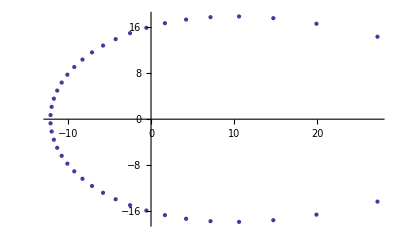

```mathematica
ListPlot[{Re[#],Im[#]}&/@(x/.NSolve[Normal[Series[Exp[x],{x,0,40}]]==0,x])]
```

### Properties & Relations (9)

Seriespaclet:ref/Series always only keeps terms up to the specified order:

```mathematica
Series[(1+x)^10,{x,0,5}]
```

1+10 x+45 x^2+120 x^3+210 x^4+252 x^5+O[x]^6

Operations on series keep only the appropriate terms:

```mathematica
Sqrt[%]
```

1+5 x+10 x^2+10 x^3+5 x^4+x^5+O[x]^6

Normalpaclet:ref/Normal converts to an ordinary polynomial:

```mathematica
Sqrt[Normal[Series[(1+x)^10,{x,0,5}]]]
```

√(1+10 x+45 x^2+120 x^3+210 x^4+252 x^5)

Any mathematical function can be applied to a series:

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
BesselJ[0,%]^%
```

1-x^3/4+(7 x^5)/64+x^6/32-(91 x^7)/5760-(7 x^8)/256-(7445 x^9)/3096576+(3661 x^10)/368640+(77509 x^11)/22118400+O[x]^12

Adding a series of lower order causes the higher-order terms to be dropped:

```mathematica
Series[Exp[x],{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

```mathematica
%+Series[Sin[x],{x,0,5}]
```

1+2 x+x^2/2+x^4/24+x^5/60+O[x]^6

Differentiate a series:

```mathematica
D[Series[Tan[x],{x,0,10}],x]
```

1+x^2+(2 x^4)/3+(17 x^6)/45+(62 x^8)/315+O[x]^10

Solve equations for series coefficients:

```mathematica
Series[a Sin[x]+b Sin[2 x],{x,0,3}]==Series[Sinh[x],{x,0,3}]
```

(a+2 b) x+(-a/6-(4 b)/3) x^3+O[x]^4==x+x^3/6+O[x]^4

```mathematica
Solve[%,{a,b}]
```

{{a→5/3,b→-1/3}}

Find the list of coefficients in a series:

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
CoefficientList[%,x]
```

{0,1,0,-1/6,0,1/120,0,-1/5040,0,1/362880}

Use Opaclet:ref/O[x] to force the construction of a series:

```mathematica
Sin[x] + O[x]^10
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^10

ComposeSeriespaclet:ref/ComposeSeries treats a series as a function to apply to another series:

```mathematica
ComposeSeries[x+2x^2+O[x]^10,Series[Exp[x]-1,{x,0,10}]]
```

x+(5 x^2)/2+(13 x^3)/6+(29 x^4)/24+(61 x^5)/120+(25 x^6)/144+(253 x^7)/5040+(509 x^8)/40320+(1021 x^9)/362880+O[x]^10

InverseSeriespaclet:ref/InverseSeries does series reversion to find the series for the inverse function of a series:

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
InverseSeries[%,x]
```

x+x^3/6+(3 x^5)/40+(5 x^7)/112+(35 x^9)/1152+O[x]^11

```mathematica
Series[ArcSin[x],{x,0,10}]
```

x+x^3/6+(3 x^5)/40+(5 x^7)/112+(35 x^9)/1152+O[x]^11

### Possible Issues (7)

When there is an essential singularity, Seriespaclet:ref/Series will attempt to factor it out:

```mathematica
Series[Sin[1/x],{x,0,1}]
```

Sin[1/x]

```mathematica
Series[Sin[1/x] Sin[x],{x,0,10}]
```

(x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11) Sin[1/x]

Numeric values cannot be substituted directly for the expansion variable in a series:

```mathematica
Series[Exp[x],{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

```mathematica
%/.x->1
```

SeriesData::ssdn: Attempt to evaluate a series at the number 1. Returning Indeterminate.

Indeterminate

Use Normalpaclet:ref/Normal to get a normal expression in which the substitution can be done:

```mathematica
Normal[Series[Exp[x],{x,0,10}]]/.x->1
```

9864101/3628800

Series must be converted to normal expressions before being plotted:

```mathematica
Plot[Evaluate[Normal[Series[Sin[x],{x,0,10}]]],{x,0,2Pi}]
```

-Graphics-

Power series with different expansion points cannot be combined:

```mathematica
Series[Exp[x],{x,1,3}] + Series[Exp[x],{x,0,3}]
```

Series::icm: Series in x to be combined have unequal expansion points 0 and 1.

(1+x+x^2/2+x^3/6+O[x]^4)+(ⅇ+ⅇ (x-1)+1/2 ⅇ (x-1)^2+1/6 ⅇ (x-1)^3+O[x-1]^4)

Not all series are represented by expressions with head SeriesDatapaclet:ref/SeriesData:

```mathematica
Series[x^a Exp[x],{x,0,5}]
```

x^a (1+x+x^2/2+x^3/6+x^4/24+x^5/120+O[x]^6)

```mathematica
InputForm[%]
```

x^a*SeriesData[x, 0, {1, 1, 1/2, 1/6, 1/24, 1/120}, 0, 6, 1]

Some functions cannot be decomposed into series of power-like functions:

```mathematica
Series[Zeta[x],{x,Infinity,10}]
```

1+2^-x+3^-x+4^-x+5^-x+6^-x+7^-x+8^-x+9^-x+10^-x

Seriespaclet:ref/Series does not change expressions independent of the expansion variable:

```mathematica
Series[0,{x,0,4}]
```

0

```mathematica
Series[Sin[y],{x,0,4}]
```

Sin[y]

## See Also

SeriesCoefficientpaclet:ref/SeriesCoefficient  ▪  InverseSeriespaclet:ref/InverseSeries  ▪  ComposeSeriespaclet:ref/ComposeSeries  ▪  Limitpaclet:ref/Limit  ▪  Normalpaclet:ref/Normal  ▪  InverseZTransformpaclet:ref/InverseZTransform  ▪  RSolvepaclet:ref/RSolve  ▪  Opaclet:ref/O  ▪  SeriesDatapaclet:ref/SeriesData  ▪  PadeApproximantpaclet:ref/PadeApproximant  ▪  FourierSeriespaclet:ref/FourierSeries

## Tutorials

Symbolic Mathematics: Basic Operationspaclet:tutorial/SymbolicCalculations

Power Seriespaclet:tutorial/PowerSeries

Making Power Series Expansionspaclet:tutorial/MakingPowerSeriesExpansions

Operations on Power Seriespaclet:tutorial/OperationsOnPowerSeries

The Representation of Power Seriespaclet:tutorial/TheRepresentationOfPowerSeries

Converting Power Series to Normal Expressionspaclet:tutorial/ConvertingPowerSeriesToNormalExpressions

## Related Guides

Analytic Number Theorypaclet:guide/AnalyticNumberTheory

Calculuspaclet:guide/Calculus

Manipulating Equationspaclet:guide/ManipulatingEquations

Multiplicative Number Theorypaclet:guide/MultiplicativeNumberTheory

Series Expansionspaclet:guide/SeriesExpansions

New in 6.0: Mathematics & Algorithmspaclet:guide/NewIn60MathematicsAndAlgorithms

## Related Links

Demonstrations with Serieshttp://demonstrations.wolfram.com/symbol.html?symbol=Series (Wolfram Demonstrations Projecthttp://demonstrations.wolfram.com/)

Implementation notes: Algebra and Calculuspaclet:tutorial/SomeNotesOnInternalImplementation#26477

NKS|Onlinehttp://www.wolframscience.com/nksonline/index/search.cgi?SearchIndex=Series (A New Kind of Sciencehttp://www.wolframscience.com/nksonline/)